# 2. domača naloga 2025/26 - 1.del

## 1. naloga

a) Izračunajte neskončno vsoto 1+1/9+1/25+1/49+1/81+...
b) Izračunajte limito funkcije 
		f(x) = (sin(x)-x)/x^3,
    ko gre x proti 0.
c) Izračunajte ploščino lika, ki ga omejujejo graf funkcije g(x) = sin(x)+x^2, abscisna os ter navpičnici x=0 in x=2π.
d) Izračunajte ploščino lika, ki ga omejujeta grafa funkcij g(x) = sin(x)+x^2 in g1(x) = sin(x) + x^5/5.

```mathematica
Sum[1/(2n+1)^2,{n,0,Infinity}]
```

π^2/8

```mathematica
Limit[(Sin[x]-x)/x^3,x->0]
```

-1/6

```mathematica
Integrate[Sin[x]+x^2,{x,0,2 Pi}]
```

(8 π^3)/3

```mathematica
Integrate[(Sin[x]+x^2)-(Sin[x]+x^5/5),{x,0,5^(1/3)}]
```

5/6

## 2. naloga

a)  Definirajte funkcijo A(m,n), ki sprejme naravni števili  in  in vrne matriko dimenzije , kjer se na vsakem mestu v matriki pojavi vsota indeksa stolpca in indeksa vrstice.
b) Izračunajte determinanto, rang in lastne vrednosti matrike . Kaj opazite?
c)  Narišite vektorje, ki ustrezajo stolpcem matrike . S pomočjo ukaza InfinitePlane na sliko narišite še ravnino, v kateri ti trije vektorji ležijo. 
d) Določite parametra, s katerima lahko prvi stolpec matrike A(3,3) izrazimo z drugima dvema.
e) Določite cela števila α, x_1,x_2 in x_3, ki zadoščajo enakosti 
		M (x_1
x_2
x_3) = (-3
-5
-9
-11) ,
    kjer je M matrika, podana kot A(4,3)+αI, kjer I označuje identično matriko ustrezne velikosti. Rešitev zapišite v eni vrstici.

```mathematica
A[n_,m_]:=Table[i+j,{i,1,n},{j,1,m}]
```

```mathematica
Det[A[3,3]]
MatrixRank[A[3,3]]
Eigenvalues[A[3,3]]
```

0

2

{6+√42,6-√42,0}

```mathematica
Graphics3D[{Arrow[{{0,0,0},#}]&/@Transpose[A[3,3]],Opacity[0.5],InfinitePlane[{{0,0,0},A[3,3][[All,1]],A[3,3][[All,2]]}]}]
```

-Graphics3D-

## 3. naloga

V datoteki ‘vreme.xlsx’ se nahajajo podatki o najvišjih in povprečnih mesečnih temperaturah v Ljubljani v letu 2025. Podatke uvozite v Mathematico.

a) Grafično predstavite podatke o najvišjih mesečnih temperaturah (graf naj bo čim bolj podoben spodnjemu). Pri tem vrednosti temperatur in številke mesecev z ustreznimi poizvedbami preberite iz uvožene tabele.
b) Napišite poizvedbo, ki bo vrnila imena ‘toplih mesecev’ - to so tisti meseci, katerih povprečna temperatura je višja ob 15 stopinj. Poizvedbo poskusite napisati v eni vrstici.

```mathematica
BarChart[vreme[[All,"Najvisja_Temperatura"]],ChartLabels->vreme[[All,"Mesec"]],PlotLabel->"Mesečne najvišje temperature v Ljubljani leta 2025"]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

BarChart::ldata: Symbol[] is not a valid dataset or list of datasets.

BarChart[Symbol[],ChartLabels→Symbol[],PlotLabel→Mesečne najvišje temperature v Ljubljani leta 2025]

```mathematica
Select[vreme,#[[3]]>15&][[All,1]]
```

Select::normal: Nonatomic expression expected at position 1 in Select[vreme,#1⟦3⟧>15&].

Part::partd: Part specification Select[vreme,#1⟦3⟧>15&]⟦All,1⟧ is longer than depth of object.

Select[vreme,#1⟦3⟧>15&]⟦All,1⟧

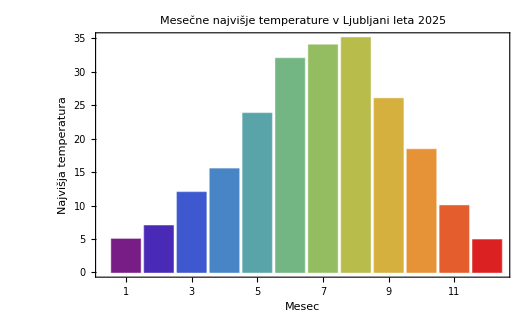

```mathematica
BarChart[vreme[[All,"Najvisja_Temperatura"]],ChartLabels->vreme[[All,"Mesec"]],PlotLabel->"Mesečne najvišje temperature v Ljubljani leta 2025"]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

BarChart::ldata: Symbol[] is not a valid dataset or list of datasets.

BarChart[Symbol[],ChartLabels→Symbol[],PlotLabel→Mesečne najvišje temperature v Ljubljani leta 2025]

```mathematica
Select[vreme,#[[3]]>15&][[All,1]]
```

Select::normal: Nonatomic expression expected at position 1 in Select[vreme,#1⟦3⟧>15&].

Part::partd: Part specification Select[vreme,#1⟦3⟧>15&]⟦All,1⟧ is longer than depth of object.

Select[vreme,#1⟦3⟧>15&]⟦All,1⟧

Import::nffil: File vreme.xlsx not found during Import.

Rest::normal: Nonatomic expression expected at position 1 in Rest[$Failed].

Part::partd: Part specification Rest[$Failed]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification Rest[$Failed]⟦All,1⟧ is longer than depth of object.

BarChart::ldata: Rest[$Failed]⟦All,2⟧ is not a valid dataset or list of datasets.

Part::partd: Part specification $Failed⟦3⟧ is longer than depth of object.

Rest::argx: Rest called with 0 arguments; 1 argument is expected.

Select::normal: Nonatomic expression expected at position 1 in Select[vreme,#1⟦3⟧>15&].

Part::partd: Part specification Select[vreme,#1⟦3⟧>15&]⟦All,1⟧ is longer than depth of object.